No CRN: 3 out of 51

No CRN: 6 out of 51

No CRN: 9 out of 51

No CRN: 12 out of 51

No CRN: 15 out of 51

No CRN: 18 out of 51

No CRN: 21 out of 51

No CRN: 24 out of 51

No CRN: 27 out of 51

No CRN: 30 out of 51

No CRN: 33 out of 51

No CRN: 36 out of 51

No CRN: 39 out of 51

No CRN: 42 out of 51

No CRN: 45 out of 51

No CRN: 48 out of 51

No CRN: 51 out of 51

Starting push-out estimator

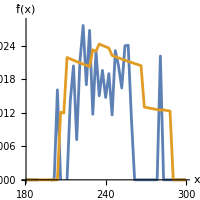

No CRN: 3 out of 51

No CRN: 6 out of 51

No CRN: 9 out of 51

No CRN: 12 out of 51

No CRN: 15 out of 51

No CRN: 18 out of 51

No CRN: 21 out of 51

No CRN: 24 out of 51

No CRN: 27 out of 51

No CRN: 30 out of 51

No CRN: 33 out of 51

No CRN: 36 out of 51

No CRN: 39 out of 51

No CRN: 42 out of 51

No CRN: 45 out of 51

No CRN: 48 out of 51

No CRN: 51 out of 51

Starting push-out estimator

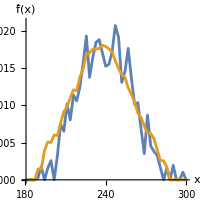

No CRN: 3 out of 51

No CRN: 6 out of 51

No CRN: 9 out of 51

No CRN: 12 out of 51

No CRN: 15 out of 51

No CRN: 18 out of 51

No CRN: 21 out of 51

No CRN: 24 out of 51

No CRN: 27 out of 51

No CRN: 30 out of 51

No CRN: 33 out of 51

No CRN: 36 out of 51

No CRN: 39 out of 51

No CRN: 42 out of 51

No CRN: 45 out of 51

No CRN: 48 out of 51

No CRN: 51 out of 51

Starting push-out estimator

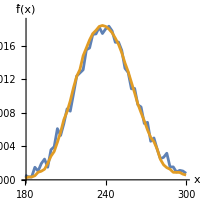

No CRN: 3 out of 51

No CRN: 6 out of 51

No CRN: 9 out of 51

No CRN: 12 out of 51

No CRN: 15 out of 51

No CRN: 18 out of 51

No CRN: 21 out of 51

No CRN: 24 out of 51

No CRN: 27 out of 51

No CRN: 30 out of 51

No CRN: 33 out of 51

No CRN: 36 out of 51

No CRN: 39 out of 51

No CRN: 42 out of 51

No CRN: 45 out of 51

No CRN: 48 out of 51

No CRN: 51 out of 51

Starting push-out estimator

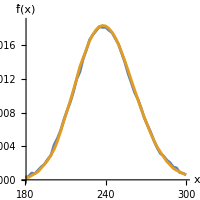

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SetDirectory[NotebookDirectory[]];

GetCopulaInfo[Copula_]:=Module[{ϕ,ψ,ZDist,CopulaName,θ},
ZDist=None;
If[Copula=!="Product",
{CopulaName,θ}=Copula;
Switch[CopulaName,
"Clayton",
ϕ[u_]=(1+u/θ)^-θ;
ψ[u_]=θ (u^(-1/θ)-1);
ZDist=GammaDistribution[θ,1/θ];
,
"Frank",
ϕ[u_]=1/Log[θ] Log[1+Exp[-u] (Exp[Log[θ]]-1)];
ψ[u_]=-Log[ (Exp[Log[θ] u] - 1)/(Exp[Log[θ]]-1)],
"GumbelHougaard",
ϕ[u_]=Exp[-u^(1/θ)];
ψ[u_]=(-Log[u])^θ;
ZDist=StableDistribution[1,1/θ,1,0,Cos[Pi /(2θ)]^θ],
_,
ϕ=None;ψ=None
]];
{ϕ,ψ,ZDist}
];

{Copula,Marg,n,sRange}={"Product",GammaDistribution[3,2],40,{180,300}};


NumPoints=50;

SeedRandom[1];

(* If given a list of marginals use them, otherwise take marginals to be identically distributed *)
Margs=If[ListQ[Marg], Marg, ConstantArray[Marg,n]];

(* Extract the simple form for the pdfs/cdfs assuming the input is inside the relevant support. *)
LBs=Table[Quantile[Margs[[i]],0],{i,n}];UBs=Table[Quantile[Margs[[i]],1],{i,n}];
PDFs=Table[Refine[PDF[Margs[[i]],Subscript[x, i]],Subscript[x, i]>LBs[[i]]&&Subscript[x, i]<UBs[[i]]],{i,n}];
CDFs=Table[Refine[CDF[Margs[[i]],Subscript[x, i]],Subscript[x, i]>LBs[[i]]&&Subscript[x, i]<UBs[[i]]],{i,n}];

XDist=CopulaDistribution[Copula,Margs];
{ϕ,ψ,ZDist}=GetCopulaInfo[Copula];

(* Create useful booleans for: i) is this the independent case, ii) does this copula have a Marshall-Olkin respresentation. *)
IsIndCopula=(Copula=== "Product");
HasMOForm=(ZDist=!=None);

ss= Range[sRange[[1]],sRange[[2]],(sRange[[2]]-sRange[[1]])/NumPoints]//DeleteCases[#,0]&;

(* Calculate the pdf of X using properties of Archimedean copulas *)
CPDF=If[IsIndCopula,1,
(D[ϕ[t],{t,n}]/.{t-> Sum[ψ[Subscript[u, i]],{i,n}]})*Product[ψ'[Subscript[u, i]],{i,n}]
];
IndPDF=Product[PDFs[[i]],{i,n}];
FullPDF=IndPDF*CPDF;
FullPDF=FullPDF/.Table[Subscript[u, i]->CDFs[[i]],{i,n}];


Plots=Table[
(***************************** Not using CRN *****************************)

OursNoCRN=Table[
If[Mod[i,3]== 0,Print["No CRN: " , i," out of ", Length[ss]]];
s=ss[[i]];

RVs=RandomVariate[XDist,R];
Sums=Total/@RVs;

(* Perform the push-out estimator *)
POPDF=FullPDF/.Table[Subscript[u, i]->CDFs[[i]],{i,n}];

(* Calculate the gradient of the log density at each replicate point.  *)
Derivs=Grad[Log[POPDF],Table[Subscript[x, i],{i,n}]];

Repl=Flatten@{
Table[{
If[!FreeQ[Derivs,Subscript[u, i]],{Subscript[u, i][Subscript[x, i]]->CDF[Margs[[i]],RVs[[;;,i]]],Subscript[u, i]'[Subscript[x, i]]->PDF[Margs[[i]],RVs[[;;,i]]]},{}],
If[!FreeQ[Derivs,Subscript[x, i]],Subscript[x, i]->RVs[[;;,i]],{}]
},{i,n}]
};

M=Transpose[Derivs/.Repl];
Grads=Table[RVs[[i]].M[[i]],{i,R}]+n;

(* Construct the two versions of the estimator, then make the approximately optimal mixture of them. *)
Inds= Table[Boole[Sr ≤ s],{Sr,Sums}];
Lefts= Grads *Inds/s;
Rights=- Grads * (1-Inds)/s;

PilotSize=Max[3,Ceiling[0.05*R]];
CC=Covariance[Transpose@{Lefts[[;;PilotSize]],Rights[[;;PilotSize]]}];
p=(CC[[2,2]]-CC[[1,2]])/(CC[[1,1]]+CC[[2,2]]-2CC[[1,2]]);

OurNoCRNEsts= p*Lefts[[PilotSize+1;;]]+(1-p)Rights[[PilotSize+1;;]];

Mean[OurNoCRNEsts]
,{i,Length[ss]}];

(***************************** Using CRN *****************************)

RVs=RandomVariate[XDist,R];
Sums=Total/@RVs;

(* Perform the push-out estimator *)
Print["Starting push-out estimator"];
POPDF=FullPDF/.Table[Subscript[u, i]->CDFs[[i]],{i,n}];

(* Calculate the gradient of the log density at each replicate point.  *)
Derivs=Grad[Log[POPDF],Table[Subscript[x, i],{i,n}]];

Repl=Flatten@{
Table[{
If[!FreeQ[Derivs,Subscript[u, i]],{Subscript[u, i][Subscript[x, i]]->CDF[Margs[[i]],RVs[[;;,i]]],Subscript[u, i]'[Subscript[x, i]]->PDF[Margs[[i]],RVs[[;;,i]]]},{}],
If[!FreeQ[Derivs,Subscript[x, i]],Subscript[x, i]->RVs[[;;,i]],{}]
},{i,n}]
};

M=Transpose[Derivs/.Repl];
Grads=Table[RVs[[i]].M[[i]],{i,R}]+n;

(* Construct the two versions of the estimator, then make the approximately optimal mixture of them. *)
OurEsts=Table[
Inds= Table[Boole[Sr ≤ s],{Sr,Sums}];
Lefts= Grads *Inds/s;
Rights=- Grads * (1-Inds)/s;

PilotSize=Max[3,Ceiling[0.05*R]];
CC=Covariance[Transpose@{Lefts[[;;PilotSize]],Rights[[;;PilotSize]]}];
p=(CC[[2,2]]-CC[[1,2]])/(CC[[1,1]]+CC[[2,2]]-2CC[[1,2]]);

p*Lefts[[PilotSize+1;;]]+(1-p)Rights[[PilotSize+1;;]]
,{s,ss}];

{Ours,OurVars}=({Mean[#],Variance[#]}&/@OurEsts)ᵀ;


(* Setup for plotting *)
WithS[Data_]:=Transpose[{ss,Data}];
Colours=Lookup["DefaultPlotStyle"]@Lookup[Method]@Charting`ResolvePlotTheme[Automatic,Plot];

(* Create the plot of the estimates and for the relative errors. *)
EstimatorNames={"RN","CRN"};

EstimatesPlot=
ListPlot[{WithS[OursNoCRN],WithS[Ours]},Joined->True,PlotStyle->Thickness[0.010],
AspectRatio->1,AxesLabel-> {"x","f̂(x)"},ImageSize-> {200,200} ,PlotRange->{{Min[ss],Max[ss]},{0, Max[{Max[OursNoCRN], Max[Ours]}]*1.025 }} ]; (* 0.025 *)
Print[EstimatesPlot];
EstimatesPlot

,{R,{10,10^2,10^3,10^4}}]
```

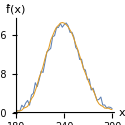

```mathematica
EstimatesPlot
```

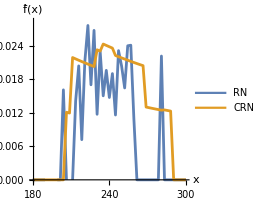
-Graphics--Graphics-
-Graphics--Graphics-

```mathematica
CombinedPlot=Legended[Column[{Row[{Plots[[1]], Plots[[2]]}],Row[{Plots[[3]],Plots[[4]]}]},Center],LineLegend[Colours,EstimatorNames]];
Print[CombinedPlot];
Export["crn.pdf",CombinedPlot];
```

```mathematica
ImageSize-> {500,125},
```

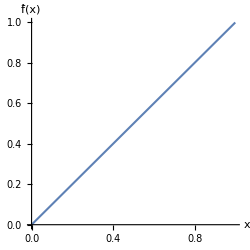

```mathematica
ImageSize-> {250,125}
```

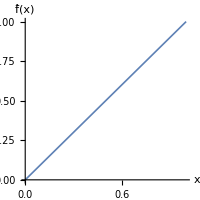

-Graphics--Graphics-
-Graphics--Graphics-

```mathematica
p=Plot[x,{x,0,1},PlotStyle->Thickness[0.006],ImageSize-> {200,200},
AspectRatio->1,AxesLabel-> {"x","f̂(x)"}]
CombinedPlot=Legended[Column[{Row[{EstimatesPlot,EstimatesPlot}],Row[{EstimatesPlot,EstimatesPlot}]},Center],LineLegend[Colours,EstimatorNames]];
Print[CombinedPlot];
Export["crn.pdf",CombinedPlot];
```